# Input

```mathematica
brb=0.578;brtau=0.0637;brmu=2.21 10^-4;brs=4.4 10^-4;brc=2.68 10^-2;brg=8.56 10^-2;brgamma=2.30 10^-3;brw=0.216;brz=0.0267;
brzgamma=1.533*10^-3;
```

## MuC @ 3 TeV

```mathematica
higgsobsMuC310p[kz_,kw_,kg_,kgamma_,kb_,kt_,kc_,ktau_,kmu_,brinv_,ktotal_]:={kw^2 kb^2/ktotal,kw^2 kc^2/ktotal,kw^2 kg^2/ktotal,kw^2 ktau^2/ktotal,kw^2 kw^2/ktotal,kw^2 kw^2/ktotal,kw^2 kz^2/ktotal,kw^2 kz^2/ktotal,kw^2 kz^2/ktotal,kw^2 kgamma^2/ktotal(*,kw^2 kzgamma^2/ktotal*),kw^2 kmu^2/ktotal,kz^2 kb^2/ktotal,kz^2 kc^2/ktotal,kz^2 kg^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kw^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kgamma^2/ktotal(*,kt^2 kb^2/ktotal*)(*adding ttH *),kz^2,kz^2brinv+1};
(*adding ttH so that the fit closed*)
higgspreMuC3={0.8,12,2.8,3.8,1.6,5.4,48,12,65,6.4(*,45*),28,2.6,72,14,21,8.4,17,34,23(*,61*)(*adding ttH *),3.94,0.2*Sqrt[2]}/100;
inputcorrelationsMuC3=(*06/14/2023*)IdentityMatrix[21]*100(*+halfcorrelationᵀ+halfcorrelation*);
inverseinputcorrelationsMuC3=Inverse[inputcorrelationsMuC3/100];
chisquarehtt3[kw_,kz_,kt_]:=2.2*10^2(kw*kt-1)^2+2.9*(kz*kt-1)^2-23*(kw*kt-1)(kz*kt-1)-1.2*10^3(kw*kt-1)^3+10*(kz*kt-1)^3+92*(kw*kt-1)^2(kz*kt-1)-1.3*10^2(kw*kt-1)(kz*kt-1)^2+3.1*10^3*(kw*kt-1)^4+38*(kz*kt-1)^4+6.9*10^2(kw*kt-1)^2(kz*kt-1)^2;
chisquareMuC310p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC310p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC3[[i]])((higgsobsMuC310p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC3[[j]])inverseinputcorrelationsMuC3[[i,j]]/lumif,{i,1,Length[higgspreMuC3]},{j,1,Length[higgspreMuC3]}]+chisquarehtt3[kw,kz,kt]
```

## MuC @ 10 TeV

```mathematica
higgsobsMuC1010p[kz_,kw_,kg_,kgamma_,kb_,kt_,kc_,ktau_,kmu_,brinv_,ktotal_]:={kw^2 kb^2/ktotal,kw^2 kc^2/ktotal,kw^2 kg^2/ktotal,kw^2 ktau^2/ktotal,kw^2 kw^2/ktotal,kw^2 kw^2/ktotal,kw^2 kz^2/ktotal,kw^2 kz^2/ktotal,kw^2 kz^2/ktotal,kw^2 kgamma^2/ktotal(*,kw^2 kzgamma^2/ktotal*),kw^2 kmu^2/ktotal,kz^2 kb^2/ktotal,kz^2 kc^2/ktotal,kz^2 kg^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kw^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kgamma^2/ktotal,kz^2,kz^2brinv+1};
higgspreMuC10={0.22,3.6,0.79,1.1,0.42,1.2,13,3.4,15,1.7(*,12*),5.7,0.77,17,3.3,4.8,2.0,4.4,11,4.8,0.75,0.05}/100;
inputcorrelationsMuC10=(*06/14/2023*)IdentityMatrix[21]*100(*+halfcorrelationᵀ+halfcorrelation*);
inverseinputcorrelationsMuC10=Inverse[inputcorrelationsMuC10/100];
chisquarehtt10[kw_,kz_,kt_]:=6.2*10^3(kw*kt-1)^2+1*10^2*(kz*kt-1)^2-6.6*10^2(kw*kt-1)(kz*kt-1)-4.7*10^4(kw*kt-1)^3+4.4*10^2(kz*kt-1)^3+4.0*10^3(kw*kt-1)^2(kz*kt-1)-5.1*10^3(kw*kt-1)(kz*kt-1)^2+2.1*10^5*(kw*kt-1)^4+2.6*10^3(kz*kt-1)^4+4.7*10^4(kw*kt-1)^2(kz*kt-1)^2;
chisquareMuC1010p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC10[[i]])((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC10[[j]])inverseinputcorrelationsMuC10[[i,j]]/lumif,{i,1,Length[higgspreMuC10]},{j,1,Length[higgspreMuC10]}]+chisquarehtt10[kw,kz,kt]
```

## MuC @ 125 GeV

```mathematica
higgsobsMuC12510p[kz_,kw_,kg_,kgamma_,kb_,kt_,kc_,ktau_,kmu_,brinv_,ktotal_]:={kmu^2 kmu^2/ktotal,kmu^2 ktau^2/ktotal,kmu^2 kgamma^2/ktotal,kmu^2 kw^2/ktotal,kmu^2 kz^2/ktotal,kmu^2 kg^2/ktotal,kmu^2 kt^2/ktotal,kmu^2 kb^2/ktotal,ktotal,ktotal};
higgspreMuC125={Infinity,2.4,94,0.84,2.9,5.3,12,1.03,3.22,2.80}/100;
halfcorrelationMuC125=SparseArray[{{4,10}->0.625,{8,9}->0.762,{10,10}->0}]//Normal;
inputcorrelationsMuC125 = IdentityMatrix[10]*100+halfcorrelationMuC125ᵀ+halfcorrelationMuC125;
inverseinputcorrelationsMuC125=Inverse[inputcorrelationsMuC125/100];
chisquareMuC12510p[{kz_,kw_,kg_,kgamma_,kb_,kt_,kc_,ktau_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC12510p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreMuC125[[i]])((higgsobsMuC12510p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreMuC125[[j]])inverseinputcorrelationsMuC125[[i,j]]/lumif,{i,1,Length[higgspreMuC125]},{j,1,Length[higgspreMuC125]}]
```

## HL-LHC

```mathematica
higgsobsLHC10p[kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_]:={kg^2 kgamma^2/ktotal,kg^2 kz^2/ktotal,kg^2 kw^2/ktotal,kg^2 ktau^2/ktotal,kg^2 kb^2/ktotal,kg^2 kmu^2/ktotal,8/11 kw^2 kgamma^2/ktotal+3/11 kz^2 kgamma^2/ktotal,8/11 kw^2 kz^2/ktotal+3/11 kz^2 kz^2/ktotal,8/11 kw^2 kw^2/ktotal+3/11 kz^2 kw^2/ktotal,8/11 kw^2 ktau^2/ktotal+3/11 kz^2 ktau^2/ktotal,8/11 kw^2 kmu^2/ktotal+3/11 kz^2 kmu^2/ktotal,8/11 kw^2 kz^2/ktotal+3/11 kz^2 kz^2/ktotal,kw^2 kgamma^2/ktotal,kw^2 kz^2/ktotal,kw^2 kw^2/ktotal,kw^2 kb^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^2 kb^2/ktotal,kt^2 kgamma^2/ktotal,kt^2 kz^2/ktotal,kt^2 kw^2/ktotal,kt^2 kb^2/ktotal,kt^2 ktau^2/ktotal,3/11kz^2brinv+8/11kw^2brinv+1};
higgspreLHC={4.2,4.0,3.7,5.5,24.7,13.8,12.8,13.4,7.3,4.4,54.0,13.9,47.8,13.8,9.4,23.3,78.6,18.4,6.5,9.4,24.6,9.7,11.6,14.9,2.2}/100;
halfcorrelationLHC=({{0, 48, 54, 46, -1, 14, -18, 2, -1, 2, 1, 0, 1, 2, 0, -3, 3, 6, 2, 8, 0, 2, 0, 1, 0}, {0, 0, 52, 37, -1, 13, 0, -11, -3, 0, -1, 1, 1, 1, -1, 1, -9, 6, 2, 1, 5, 1, 0, 1, 0}, {0, 0, 0, 42, -1, 15, -1, -2, -9, -1, -1, 1, 0, 0, 0, 0, -1, 10, 2, 1, 0, 2, 0, 1, 0}, {0, 0, 0, 0, -1, 11, 12, 5, 2, -16, 2, 5, 1, 2, 0, 5, 5, 5, 2, 3, 0, 1, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, -2, 0, 0, 0, -1, -1, 0, -1, -1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -1, 0, -53, 1, 0, 0, 0, 0, 1, 2, 0, 1, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 5, 6, 8, 1, 3, 0, 1, 0, 2, 2, 1, 0, 1, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 7, 7, 3, 2, 0, 1, 0, 2, 6, 0, 0, 1, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 10, 1, 2, 0, 5, 0, 1, 0, 4, 0, 1, 0, 1, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 2, 4, 1, 3, 0, 2, 1, 1, 0, 2, 1, 2, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, -33, 1, 0, 0, -5, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -68, 0, 0, 0, -1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, -1, 0, 1, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, -1, -6, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 1, -10, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -8, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 8, 18, 16, 11, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 5, 2, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 14, -7, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 9, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});(*07/27/2023*)
inputcorrelationsLHC = (*07/27/2023*)IdentityMatrix[25]*100+halfcorrelationLHCᵀ+halfcorrelationLHC;
inverseinputcorrelationsLHC=Inverse[inputcorrelationsLHC/100];
chisquareLHC10p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHC[[i]])((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHC[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHC]},{j,1,Length[higgspreLHC]}]
```

## CEPC @ 240 GeV

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,(*kt_,*)kc_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kc^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
higgsprecepc=(*Apr.04.2022; Note that the second to last entry is infinity to avoid double counting*){6.36,0.42,3.02,0.53,4.17,0.81,2.02,0.14,1.59,(*Infinity*)(0.00401209+0.00402172)*100/2,0.26,0.07}/100;
(*higgsobscepcinv=0.07/100;*)
halfcorrelationcepc=(*Apr.15.2018*)SparseArray[{{12,12}->0,{4,2}->-13.286,{5,2}->-6.669,{6,2}->0.864,{7,2}->0.638,{8,2}->-0.025,{9,2}->-0.011,{10,2}->-0.075,{5,4}->-32.350,{6,4}->-3.644,{7,4}->-2.869,{8,4}->1.140,{9,4}->-0.521,{10,4}->0.328,{6,5}->-1.926,{7,5}->-1.167,{8,5}->-1.809,{9,5}->0.827,{10,5}->0.148,{7,6}->-22.332,{8,6}->-12.429,{9,6}-> 5.681,{10,6}->-1.680,{8,7}-> -7.027,{9,7}-> 3.212,{10,7}-> -6.498,{9,8}-> -45.706,{10,8}-> 0.918,{10,9}-> -0.420}]//Normal;
inputcorrelationscepc=(*Apr.15.2018*)IdentityMatrix[12]*100+halfcorrelationcepcᵀ+halfcorrelationcepc;
inverseinputcorrelationscepc=Inverse[inputcorrelationscepc/100];
chisquarecepc10p[{kb_,(*kt_,*)kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelationscepc[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]
```

## CEPC @ 240GeV+360 GeV

```mathematica
higgsobscepc36010p[kz_,kw_,kg_,kgamma_,kb_,(*kt_,*)kc_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kc^2/ktotal,kz^2 kb^2/ktotal,kz^2,kw^2 kmu^2/ktotal,kw^2 ktau^2/ktotal,kw^2 kgamma^2/ktotal,kw^2 kw^2/ktotal,kw^2 kz^2/ktotal,kw^2 kg^2/ktotal,kw^2 kc^2/ktotal,kw^2 kb^2/ktotal,kz^2 kw^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kg^2/ktotal,kz^2 kc^2/ktotal,kz^2 kb^2/ktotal};
higgsprecepc360={41,2.1,11,2.80,20,3.40,8.80,0.90,1.40,57,4.2,16,4.4,21,4.5,16,1.10,6.5,7.5,12,20,4.3}/100;
inputcorrelationscepc360=IdentityMatrix[22]*100;
inverseinputcorrelationscepc360=Inverse[inputcorrelationscepc360/100];
chisquarecepc36010p[{kb_,(*kt_,*)kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelationscepc[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc360[[i]])((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc360[[j]])inverseinputcorrelationscepc360[[i,j]]/lumif,{i,1,Length[higgsprecepc360]},{j,1,Length[higgsprecepc360]}]
```

## Combined Chi square

```mathematica
chisquareMuC3LHC10p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC310p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC3[[i]])((higgsobsMuC310p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC3[[j]])inverseinputcorrelationsMuC3[[i,j]]/lumif,{i,1,Length[higgspreMuC3]},{j,1,Length[higgspreMuC3]}]+chisquarehtt3[kw,kz,kt]+Sum[((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHC[[i]])((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHC[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHC]},{j,1,Length[higgspreLHC]}]
chisquareMuC10LHC10p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC10[[i]])((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC10[[j]])inverseinputcorrelationsMuC10[[i,j]]/lumif,{i,1,Length[higgspreMuC10]},{j,1,Length[higgspreMuC10]}]+chisquarehtt10[kw,kz,kt]+Sum[((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHC[[i]])((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHC[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHC]},{j,1,Length[higgspreLHC]}]

chisquarecepcLHC10p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelationscepc[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHC[[i]])((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHC[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHC]},{j,1,Length[higgspreLHC]}]
chisquarecepc360LHC10p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelationscepc[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc360[[i]])((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc360[[j]])inverseinputcorrelationscepc360[[i,j]]/lumif,{i,1,Length[higgsprecepc360]},{j,1,Length[higgsprecepc360]}]+Sum[((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHC[[i]])((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHC[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHC]},{j,1,Length[higgspreLHC]}]

chisquareMuC10cepcLHC10p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC10[[i]])((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC10[[j]])inverseinputcorrelationsMuC10[[i,j]]/lumif,{i,1,Length[higgspreMuC10]},{j,1,Length[higgspreMuC10]}]+chisquarehtt10[kw,kz,kt]+Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelationscepc[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHC[[i]])((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHC[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHC]},{j,1,Length[higgspreLHC]}]

chisquareMuC10cepc360LHC10p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC10[[i]])((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC10[[j]])inverseinputcorrelationsMuC10[[i,j]]/lumif,{i,1,Length[higgspreMuC10]},{j,1,Length[higgspreMuC10]}]+chisquarehtt10[kw,kz,kt]+Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelationscepc[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc360[[i]])((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc360[[j]])inverseinputcorrelationscepc360[[i,j]]/lumif,{i,1,Length[higgsprecepc360]},{j,1,Length[higgsprecepc360]}]+Sum[((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHC[[i]])((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHC[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHC]},{j,1,Length[higgspreLHC]}]
chisquareMuC3cepc360LHC10p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC310p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC3[[i]])((higgsobsMuC310p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC3[[j]])inverseinputcorrelationsMuC3[[i,j]]/lumif,{i,1,Length[higgspreMuC3]},{j,1,Length[higgspreMuC3]}]+chisquarehtt3[kw,kz,kt]+Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelationscepc[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc360[[i]])((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc360[[j]])inverseinputcorrelationscepc360[[i,j]]/lumif,{i,1,Length[higgsprecepc360]},{j,1,Length[higgsprecepc360]}]+Sum[((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHC[[i]])((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHC[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHC]},{j,1,Length[higgspreLHC]}]


chisquareMuC3MuC125cepc360LHC10p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC310p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC3[[i]])((higgsobsMuC310p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC3[[j]])inverseinputcorrelationsMuC3[[i,j]]/lumif,{i,1,Length[higgspreMuC3]},{j,1,Length[higgspreMuC3]}]+chisquarehtt3[kw,kz,kt]+Sum[((higgsobsMuC12510p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreMuC125[[i]])((higgsobsMuC12510p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreMuC125[[j]])inverseinputcorrelationsMuC125[[i,j]]/lumif,{i,1,Length[higgspreMuC125]},{j,1,Length[higgspreMuC125]}]+Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelationscepc[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc360[[i]])((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc360[[j]])inverseinputcorrelationscepc360[[i,j]]/lumif,{i,1,Length[higgsprecepc360]},{j,1,Length[higgsprecepc360]}]+Sum[((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHC[[i]])((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHC[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHC]},{j,1,Length[higgspreLHC]}]
chisquareMuC10MuC125cepc360LHC10p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC10[[i]])((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC10[[j]])inverseinputcorrelationsMuC10[[i,j]]/lumif,{i,1,Length[higgspreMuC10]},{j,1,Length[higgspreMuC10]}]+chisquarehtt10[kw,kz,kt]+Sum[((higgsobsMuC12510p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreMuC125[[i]])((higgsobsMuC12510p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreMuC125[[j]])inverseinputcorrelationsMuC125[[i,j]]/lumif,{i,1,Length[higgspreMuC125]},{j,1,Length[higgspreMuC125]}]+Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelationscepc[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc360[[i]])((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc360[[j]])inverseinputcorrelationscepc360[[i,j]]/lumif,{i,1,Length[higgsprecepc360]},{j,1,Length[higgsprecepc360]}]+Sum[((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHC[[i]])((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHC[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHC]},{j,1,Length[higgspreLHC]}]
chisquareMuC3MuC12510p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC310p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC3[[i]])((higgsobsMuC310p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC3[[j]])inverseinputcorrelationsMuC3[[i,j]]/lumif,{i,1,Length[higgspreMuC3]},{j,1,Length[higgspreMuC3]}]+chisquarehtt3[kw,kz,kt]+Sum[((higgsobsMuC12510p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreMuC125[[i]])((higgsobsMuC12510p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreMuC125[[j]])inverseinputcorrelationsMuC125[[i,j]]/lumif,{i,1,Length[higgspreMuC125]},{j,1,Length[higgspreMuC125]}]
chisquareMuC10MuC12510p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC10[[i]])((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC10[[j]])inverseinputcorrelationsMuC10[[i,j]]/lumif,{i,1,Length[higgspreMuC10]},{j,1,Length[higgspreMuC10]}]+chisquarehtt10[kw,kz,kt]+Sum[((higgsobsMuC12510p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreMuC125[[i]])((higgsobsMuC12510p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreMuC125[[j]])inverseinputcorrelationsMuC125[[i,j]]/lumif,{i,1,Length[higgspreMuC125]},{j,1,Length[higgspreMuC125]}]
```

# Fit

### 10p fit only MuC 10TeV

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistmm=Table[-RandomReal[]/20,{i,1,11}];
dlistm=Join[dlistmm[[1;;9]],{-dlistmm[[10]],dlistmm[[11]]}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC1010p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC1010p[inputlist,lumif],inputlist[[4]]≥ 0,inputlist[[4]]<2,inputlist[[8]]≥ 0,inputlist[[8]]<2,inputlist[[1]]≥ 0,inputlist[[1]]<2,inputlist[[2]]≥ 0,inputlist[[2]]<2,inputlist[[3]]≥ 0,inputlist[[3]]<2,inputlist[[6]]≥ 0,inputlist[[6]]<2, inputlist[[7]]≤2, inputlist[[7]]≥0,inputlist[[5]]≤2, inputlist[[5]]≥0, inputlist[[10]]≥0,inputlist[[10]]<1,inputlist[[9]]≥ 0, inputlist[[9]]<2,inputlist[[11]]>=(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]),inputlist[[11]]≤2},{kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}(*,MaxIterations->1000*)](*[[1]]*);Abs[chi2[[1]]-1]≥ 0.0001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2[[1]]])/(Sqrt[chi2[[1]]]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2[[1]];];
dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC1010p[inputlist,lumif],inputlist[[4]]≥ 0,inputlist[[4]]<2,inputlist[[8]]≥ 0,inputlist[[8]]<2,inputlist[[1]]≥ 0,inputlist[[1]]<2,inputlist[[2]]≥ 0,inputlist[[2]]<2,inputlist[[3]]≥ 0,inputlist[[3]]<2,inputlist[[6]]≥ 0,inputlist[[6]]<2, inputlist[[7]]≤2, inputlist[[7]]≥0,inputlist[[5]]≤2, inputlist[[5]]≥0, inputlist[[10]]≥0,inputlist[[10]]<1,inputlist[[9]]≥ 0, inputlist[[9]]<2,inputlist[[11]]>=(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]),inputlist[[11]]≤2},{kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},MaxIterations->Automatic](*[[1]]*);Abs[chi2[[1]]-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2[[1]]])/(Sqrt[chi2[[1]]]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2[[1]]];
dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC1010p//MatrixForm
MuC1010pfit=Table[MuC1010p[[i,1,1]]/2-MuC1010p[[i,1,2]]/2,{i,1,Length[MuC1010p]}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

((0.00557243
-0.00231721)
(0.0141545
-0.0136451)
(0.0183036
-0.0182288)
(0.00665206
-0.00449593)
(0.0050851
-0.00102341)
(0.00762457
-0.00594538)
(0.00374295
-0.00253552)
(0.00974268
-0.00824395)
(0.0286346
-0.0289712)
(0.000499268
0.000499267)
(0.0205838
-0.00410617))

{0.00394482,0.0138998,0.0182662,0.005574,0.00305426,0.00678497,0.00313923,0.00899332,0.0288029,2.82429×10^-10,0.012345}

```mathematica
(*{kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}*)
```

### 10p-fit-MuC10TeV-LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistmm=Table[-RandomReal[]/20,{i,1,11}];
dlistm=Join[dlistmm[[1;;9]],{-dlistmm[[10]],dlistmm[[11]]}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC10LHC10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC10LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,inputlist[[11]]>=(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC10LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,inputlist[[11]]>(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC10LHC10p//MatrixForm
MuC10LHC10pfit=Table[MuC10LHC10p[[i,1,1]]/2-MuC10LHC10p[[i,1,2]]/2,{i,1,Length[MuC10LHC10p]}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

((0.0052678
-0.00229161)
(0.0127602
-0.0122317)
(0.0182121
-0.0182145)
(0.00634236
-0.00436503)
(0.00479649
-0.00101436)
(0.00713076
-0.00553835)
(0.00365673
-0.00248709)
(0.00859986
-0.0071317)
(0.0249147
-0.0250628)
(0.00049906
0.000499058)
(0.0193809
-0.00402816))

{0.0037797,0.0124959,0.0182133,0.0053537,0.00290543,0.00633456,0.00307191,0.00786578,0.0249888,9.41362×10^-10,0.0117045}

```mathematica
MuC1010pdata={Table[If[i==Length[MuC1010pfit]-1,MuC1010pfit[[i]]*2,If[i==Length[MuC1010pfit],MuC1010pfit[[i]],MuC1010pfit[[i]]]],{i,1,Length[MuC1010pfit]}],Table[If[i==Length[MuC10LHC10pfit]-1,MuC10LHC10pfit[[i]]*2,If[i==Length[MuC10LHC10pfit],MuC10LHC10pfit[[i]],MuC10LHC10pfit[[i]]]],{i,1,Length[MuC10LHC10pfit]}]}
```

{{0.00394482,0.0138998,0.0182662,0.005574,0.00305426,0.00678497,0.00313923,0.00899332,0.0288029,5.64858×10^-10,0.012345},{0.0037797,0.0124959,0.0182133,0.0053537,0.00290543,0.00633456,0.00307191,0.00786578,0.0249888,1.88272×10^-9,0.0117045}}

### 10p fit only CEPC 240 GeV

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistm=Table[-RandomReal[]/20,{i,1,11}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[4]]^2 brw+inputlist[[6]]^2 brz+inputlist[[5]]^2 brtau+inputlist[[3]]^2 brg+inputlist[[7]]^2 brgamma+inputlist[[2]]^2 brc+inputlist[[1]]^2 brs+inputlist[[8]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[9]]), inputlist[[11]]≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal≥(inputlist[[1]]^2 brb+inputlist[[4]]^2 brw+inputlist[[6]]^2 brz+inputlist[[5]]^2 brtau+inputlist[[3]]^2 brg+inputlist[[7]]^2 brgamma+inputlist[[2]]^2 brc+inputlist[[1]]^2 brs+inputlist[[8]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[9]]), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
cepc10p//MatrixForm
cepc10pfit=Table[cepc10p[[i,1,1]]/2-cepc10p[[i,1,2]]/2,{i,1,Length[cepc10p]}]
```

NMinimize::nnum: The function value chisquarecepc10p[{1.02584,1.90094,1.4128,1.83798,1.766,0.98765,0.545925,0.821727,1.59098,1.0929,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::nnum: The function value chisquarecepc10p[{1.46719,1.01534,1.4128,1.83798,1.766,0.98765,0.545925,0.821727,1.59098,1.0929,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::nnum: The function value chisquarecepc10p[{1.46719,1.90094,1.00993,1.83798,1.766,0.98765,0.545925,0.821727,1.59098,1.0929,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::nnum: The function value chisquarecepc10p[{1.46719,1.90094,1.4128,1.0319,1.766,0.98765,0.545925,0.821727,1.59098,1.0929,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::nnum: The function value chisquarecepc10p[{1.46719,1.90094,1.4128,1.83798,1.044,0.98765,0.545925,0.821727,1.59098,1.0929,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::nnum: The function value chisquarecepc10p[{1.46719,1.90094,1.4128,1.83798,1.766,1.02479,0.545925,0.821727,1.59098,1.0929,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::nnum: The function value chisquarecepc10p[{1.46719,1.90094,1.4128,1.83798,1.766,0.98765,1.00139,0.821727,1.59098,1.0929,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::nnum: The function value chisquarecepc10p[{1.46719,1.90094,1.4128,1.83798,1.766,0.98765,0.545925,1.01582,1.59098,1.0929,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::nnum: The function value chisquarecepc10p[{0.989595,1.90094,1.4128,1.83798,1.766,0.98765,0.545925,0.821727,1.59098,1.0929,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::nnum: The function value chisquarecepc10p[{1.46719,0.977748,1.4128,1.83798,1.766,0.98765,0.545925,0.821727,1.59098,1.0929,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::nnum: The function value chisquarecepc10p[{1.46719,1.90094,0.992049,1.83798,1.766,0.98765,0.545925,0.821727,1.59098,1.0929,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::nnum: The function value chisquarecepc10p[{1.46719,1.90094,1.4128,0.989669,1.766,0.98765,0.545925,0.821727,1.59098,1.0929,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::nnum: The function value chisquarecepc10p[{1.46719,1.90094,1.4128,1.83798,0.962197,0.98765,0.545925,0.821727,1.59098,1.0929,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::nnum: The function value chisquarecepc10p[{1.46719,1.90094,1.4128,1.83798,1.766,0.971417,0.545925,0.821727,1.59098,1.0929,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::nnum: The function value chisquarecepc10p[{1.46719,1.90094,1.4128,1.83798,1.766,0.98765,0.969667,0.821727,1.59098,1.0929,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::nnum: The function value chisquarecepc10p[{1.46719,1.90094,1.4128,1.83798,1.766,0.98765,0.545925,0.963315,1.59098,1.0929,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::nnum: The function value chisquarecepc10p[{1.46719,1.90094,1.4128,1.83798,1.766,0.98765,0.545925,0.821727,1.01197,1.0929,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::nnum: The function value chisquarecepc10p[{1.46719,1.90094,1.4128,1.83798,1.766,0.98765,0.545925,0.821727,1.59098,0.0221545,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::nnum: The function value chisquarecepc10p[{1.46719,1.90094,1.4128,1.83798,1.766,0.98765,0.545925,0.821727,1.59098,1.0929,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::incst: NMinimize was unable to generate any initial points satisfying the inequality constraints {-ktotal+114.16 (0.000239+0.57844 kb^2+0.0856 kc^2+0.216 kg^2+0.000221 kgamma^2+0.0268 kt^2+0.0267 ktau^2+0.0637 kw^2+0.0023 kz^2)≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

NMinimize::nnum: The function value chisquarecepc10p[{1.46719,1.90094,1.4128,1.83798,1.766,0.98765,0.545925,0.821727,1.59098,-0.0182262,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::nnum: The function value chisquarecepc10p[{1.46719,1.90094,1.4128,1.83798,1.766,0.98765,0.545925,0.821727,1.59098,1.0929,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {1.0929,1.46719,1.4128,1.83798,0.821727,1.59098,1.90094,0.98765,1.06925,1.766,«1»}.

NMinimize::nnum: The function value chisquarecepc10p[{0.368695,0.685812,0.046972,0.557572,1.05347,1.48143,1.17046,0.570572,0.99124,0.291043,«1»},1] is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {0.291043,0.368695,0.046972,0.557572,0.570572,0.452703,0.685812,1.48143,-0.261566,1.05347,«1»}.

((0.0258449
-0.0104051)
(0.0153406
-0.0222523)
(0.00993273
-0.00795135)
(0.0319037
-0.0103309)
(0.044005
-0.0378032)
(0.024789
-0.0285825)
(0.0013851
-0.0303331)
(0.0158204
-0.036685)
(0.0119687
-0.0087596)
(0.0221545
-0.0182262)
(0.00460138
-0.00175757))

{0.018125,0.0187964,0.00894204,0.0211173,0.0409041,0.0266858,0.0158591,0.0262527,0.0103641,0.0201903,0.00317947}

### 10p-fit-CEPC240GeV+LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistm=Table[-RandomReal[]/20,{i,1,11}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepcLHC10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepcLHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepcLHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
cepcLHC10p//MatrixForm
cepcLHC10pfit=Table[cepcLHC10p[[i,1,1]]/2-cepcLHC10p[[i,1,2]]/2,{i,1,Length[cepcLHC10p]}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

((0.00608664
-0.00543143)
(0.0301914
-0.0310439)
(0.0121179
-0.0119736)
(0.00747052
-0.00708701)
(0.0062514
-0.00588372)
(0.00674917
-0.00611477)
(0.00129856
-0.00065786)
(0.0113691
-0.0112079)
(0.027012
-0.0275489)
(0.000681184
-0.000699646)
(0.013516
-0.013401))

{0.00575903,0.0306177,0.0120457,0.00727876,0.00606756,0.00643197,0.000978212,0.0112885,0.0272804,0.000690415,0.0134585}

```mathematica
cepc10pdata={Table[If[i==Length[cepc10pfit]-1,cepc10pfit[[i]]*2,If[i==Length[cepc10pfit],cepc10pfit[[i]],cepc10pfit[[i]]]],{i,1,Length[cepc10pfit]}],Table[If[i==Length[cepcLHC10pfit]-1,cepcLHC10pfit[[i]]*2,If[i==Length[cepcLHC10pfit],cepcLHC10pfit[[i]],cepcLHC10pfit[[i]]]],{i,1,Length[cepcLHC10pfit]}]}
```

{{0.018125,0.0187964,0.00894204,0.0211173,0.0409041,0.0266858,0.0158591,0.0262527,0.0103641,0.0403807,0.00317947},{0.00575903,0.0306177,0.0120457,0.00727876,0.00606756,0.00643197,0.000978212,0.0112885,0.0272804,0.00138083,0.0134585}}

### 10p-fit-CEPC240GeV+360GeV

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistmm=Table[-RandomReal[]/20,{i,1,10}];
dlistm=Join[dlistmm[[1;;8]],{-dlistmm[[9]],dlistmm[[10]]}];
arglist={kb,(*kt,*)kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc36010p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc36010p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,(*kt≥ 0,kt<2,*)kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,inputlist[[10]]≥(inputlist[[1]]^2 brb+inputlist[[4]]^2 brw+inputlist[[6]]^2 brz+inputlist[[5]]^2 brtau+inputlist[[3]]^2 brg+inputlist[[7]]^2 brgamma+inputlist[[2]]^2 brc+inputlist[[1]]^2 brs+inputlist[[8]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[9]]), inputlist[[10]]≤2},{kz,kg,kgamma,kw,kb,(*kt,*)kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc36010p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,(*kt≥ 0,kt<2,*)kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv>=0,brinv<1,kmu≥ 0, kmu<2,inputlist[[10]]≥(inputlist[[1]]^2 brb+inputlist[[4]]^2 brw+inputlist[[6]]^2 brz+inputlist[[5]]^2 brtau+inputlist[[3]]^2 brg+inputlist[[7]]^2 brgamma+inputlist[[2]]^2 brc+inputlist[[1]]^2 brs+inputlist[[8]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[9]]), inputlist[[10]]≤2},{kz,kg,kgamma,kw,kb,(*kt,*)kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc36010p//MatrixForm
cepc36010pfittemp=Table[cepc36010p[[i,1,1]]/2-cepc36010p[[i,1,2]]/2,{i,1,Length[cepc36010p]}];
cepc36010pfit={0,0,0,0,0,0,0,0,0,0,0};
cepc36010pfit[[1]]=cepc36010pfittemp[[1]];cepc36010pfit[[2]]=1.2;
Do[cepc36010pfit[[i]]=cepc36010pfittemp[[i-1]],{i,3,11}];
cepc36010pfit
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

((0.00468112
-0.00403263)
(0.0109555
-0.0108821)
(0.0063103
-0.00598713)
(0.0044211
-0.00408698)
(0.0054098
-0.00480892)
(0.00127703
-0.00064094)
(0.01502
-0.0150137)
(0.0311649
-0.031994)
(0.000680803
0.000680802)
(0.0107162
-0.00783199))

{0.00435688,1.2,0.0109188,0.00614872,0.00425404,0.00510936,0.000958984,0.0150169,0.0315795,9.59517×10^-11,0.00927409}

### 10p-fit-CEPC240GeV+360GeV+HLLHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistmm=Table[-RandomReal[]/20,{i,1,11}];
dlistm=Join[dlistmm[[1;;9]],{-dlistmm[[10]],dlistmm[[11]]}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc360LHC10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc360LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv>=0,brinv<1,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc360LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv>=0,brinv<1,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
cepc360LHC10p//MatrixForm
cepc360LHC10pfit=Table[cepc360LHC10p[[i,1,1]]/2-cepc360LHC10p[[i,1,2]]/2,{i,1,Length[cepc360LHC10p]}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

((0.00444692
-0.00380136)
(0.0301756
-0.031035)
(0.0108508
-0.0107958)
(0.00592534
-0.00561047)
(0.00417555
-0.00384069)
(0.00512173
-0.00453128)
(0.00127733
-0.000635752)
(0.0105652
-0.0104657)
(0.0264029
-0.0269837)
(0.000680374
0.000680374)
(0.010252
-0.00733132))

{0.00412414,0.0306053,0.0108233,0.00576791,0.00400812,0.00482651,0.000956541,0.0105155,0.0266933,-1.75349×10^-11,0.00879165}

```mathematica
cepc36010pdata={Table[If[i==Length[cepc36010pfit]-1,cepc36010pfit[[i]]*2,If[i==Length[cepc36010pfit],cepc36010pfit[[i]],cepc36010pfit[[i]]]],{i,1,Length[cepc36010pfit]}],Table[If[i==Length[cepc360LHC10pfit]-1,cepc360LHC10pfit[[i]]*2,If[i==Length[cepc360LHC10pfit],cepc360LHC10pfit[[i]],cepc360LHC10pfit[[i]]]],{i,1,Length[cepc360LHC10pfit]}]}
```

{{0.00435688,1.2,0.0109188,0.00614872,0.00425404,0.00510936,0.000958984,0.0150169,0.0315795,1.91903×10^-10,0.00927409},{0.00412414,0.0306053,0.0108233,0.00576791,0.00400812,0.00482651,0.000956541,0.0105155,0.0266933,-3.50698×10^-11,0.00879165}}

### MuC10TeV+CEPC240GeV+HLLHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistm=Table[-RandomReal[]/20,{i,1,11}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC10cepcLHC10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC10cepcLHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC10cepcLHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC10cepcLHC10p//MatrixForm
MuC10cepcLHC10pfit=Table[MuC10cepcLHC10p[[i,1,1]]/2-MuC10cepcLHC10p[[i,1,2]]/2,{i,1,Length[MuC10cepcLHC10p]}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

((0.0024346
-0.00172843)
(0.0127597
-0.0117744)
(0.00909258
-0.00910864)
(0.00358616
-0.00329368)
(0.00164093
-0.000917296)
(0.00323967
-0.00273365)
(0.00122424
-0.000570885)
(0.00659799
-0.00643695)
(0.0194392
-0.0197448)
(0.000402335
-0.000406798)
(0.00663758
-0.00659817))

{0.00208151,0.0122671,0.00910061,0.00343992,0.00127912,0.00298666,0.000897561,0.00651747,0.019592,0.000404567,0.00661788}

### MuC10TeV+CEPC240GeV+360GeV+HLLHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistmm=Table[-RandomReal[]/20,{i,1,11}];
dlistm=Join[dlistmm[[1;;9]],{-dlistmm[[10]],dlistmm[[11]]}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC10cepc360LHC10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC10cepc360LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv>=0,brinv<1,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC10cepc360LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv>=0,brinv<1,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC10cepc360LHC10p//MatrixForm
MuC10cepc360LHC10pfit=Table[MuC10cepc360LHC10p[[i,1,1]]/2-MuC10cepc360LHC10p[[i,1,2]]/2,{i,1,Length[MuC10cepc360LHC10p]}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

((0.00239729
-0.00170068)
(0.012759
-0.0117727)
(0.00884175
-0.00885288)
(0.00352136
-0.00323023)
(0.00161533
-0.000902616)
(0.00317771
-0.00267555)
(0.00120592
-0.000563452)
(0.00653394
-0.00637528)
(0.0193066
-0.0196087)
(0.000402211
0.0004022)
(0.00653725
-0.00292912))

{0.00204898,0.0122659,0.00884731,0.00337579,0.00125897,0.00292663,0.000884687,0.00645461,0.0194577,5.77101×10^-9,0.00473318}

### MuC3TeV+CEPC240GeV+360GeV+HLLHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistmm=Table[-RandomReal[]/20,{i,1,11}];
dlistm=Join[dlistmm[[1;;9]],{-dlistmm[[10]],dlistmm[[11]]}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC3cepc360LHC10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC3cepc360LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC3cepc360LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC3cepc360LHC10p//MatrixForm
MuC3cepc360LHC10pfit=Table[MuC3cepc360LHC10p[[i,1,1]]/2-MuC3cepc360LHC10p[[i,1,2]]/2,{i,1,Length[MuC3cepc360LHC10p]}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

((0.00362527
-0.00292236)
(0.0281011
-0.0279549)
(0.0103544
-0.0103279)
(0.0051438
-0.00484139)
(0.00293135
-0.00251555)
(0.00435412
-0.00375239)
(0.00127396
-0.000626317)
(0.00985298
-0.00975929)
(0.0258439
-0.0264229)
(0.000661258
0.000661258)
(0.00868835
-0.00539811))

{0.00327381,0.028028,0.0103411,0.0049926,0.00272345,0.00405326,0.00095014,0.00980613,0.0261334,-8.1565×10^-13,0.00704323}

### MuC3TeV+CEPC240GeV+360GeV+HLLHC+MuC125GeV

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistm=Table[-RandomReal[]/20,{i,1,11}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC3MuC125cepc360LHC10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC3MuC125cepc360LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC3MuC125cepc360LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC3MuC125cepc360LHC10p//MatrixForm
MuC3MuC125cepc360LHC10pfit=Table[MuC3MuC125cepc360LHC10p[[i,1,1]]/2-MuC3MuC125cepc360LHC10p[[i,1,2]]/2,{i,1,Length[MuC3MuC125cepc360LHC10p]}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

((0.00335295
-0.00281095)
(0.00653599
-0.00635261)
(0.00966197
-0.00966746)
(0.0049549
-0.00475598)
(0.00276623
-0.00244529)
(0.0040914
-0.00364242)
(0.00124179
-0.000622561)
(0.00798877
-0.00788806)
(0.00486614
-0.00458155)
(0.0006596
-0.000679178)
(0.00799013
-0.00517976))

{0.00308195,0.0064443,0.00966472,0.00485544,0.00260576,0.00386691,0.000932174,0.00793842,0.00472384,0.000669389,0.00658494}

### MuC10TeV+CEPC240GeV+360GeV+HLLHC+MuC125GeV

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistm=Table[-RandomReal[]/20,{i,1,11}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC10MuC125cepc360LHC10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC10MuC125cepc360LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC10MuC125cepc360LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC10MuC125cepc360LHC10p//MatrixForm
MuC10MuC125cepc360LHC10pfit=Table[MuC10MuC125cepc360LHC10p[[i,1,1]]/2-MuC10MuC125cepc360LHC10p[[i,1,2]]/2,{i,1,Length[MuC10MuC125cepc360LHC10p]}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

((0.00226609
-0.0016691)
(0.00556348
-0.00542511)
(0.00838669
-0.00840995)
(0.00344185
-0.00321157)
(0.0015296
-0.000891065)
(0.00306095
-0.00264583)
(0.00116609
-0.000562262)
(0.00584223
-0.00570871)
(0.00453891
-0.00424139)
(0.000401762
-0.000406798)
(0.00613325
-0.00286059))

{0.0019676,0.0054943,0.00839832,0.00332671,0.00121033,0.00285339,0.000864177,0.00577547,0.00439015,0.00040428,0.00449692}

```mathematica
MuC10cepc360LHC10pdata={Table[If[i==Length[MuC3cepc360LHC10pfit]-1,MuC3cepc360LHC10pfit[[i]]*2,If[i==Length[MuC3cepc360LHC10pfit],MuC3cepc360LHC10pfit[[i]],MuC3cepc360LHC10pfit[[i]]]],{i,1,Length[MuC3cepc360LHC10pfit]}],Table[If[i==Length[MuC10cepc360LHC10pfit]-1,MuC10cepc360LHC10pfit[[i]]*2,If[i==Length[MuC10cepc360LHC10pfit],MuC10cepc360LHC10pfit[[i]],MuC10cepc360LHC10pfit[[i]]]],{i,1,Length[MuC10cepc360LHC10pfit]}],Table[If[i==Length[MuC3MuC125cepc360LHC10pfit]-1,MuC3MuC125cepc360LHC10pfit[[i]]*2,If[i==Length[MuC3MuC125cepc360LHC10pfit],MuC3MuC125cepc360LHC10pfit[[i]],MuC3MuC125cepc360LHC10pfit[[i]]]],{i,1,Length[MuC3MuC125cepc360LHC10pfit]}],Table[If[i==Length[MuC10MuC125cepc360LHC10pfit]-1,MuC10MuC125cepc360LHC10pfit[[i]]*2,If[i==Length[MuC10MuC125cepc360LHC10pfit],MuC10MuC125cepc360LHC10pfit[[i]],MuC10MuC125cepc360LHC10pfit[[i]]]],{i,1,Length[MuC10MuC125cepc360LHC10pfit]}],{0,0,0,0,0,0,0,0,0,0,0}}
```

{{0.00327381,0.028028,0.0103411,0.0049926,0.00272345,0.00405326,0.00095014,0.00980613,0.0261334,-1.6313×10^-12,0.00704323},{0.00204898,0.0122659,0.00884731,0.00337579,0.00125897,0.00292663,0.000884687,0.00645461,0.0194577,1.1542×10^-8,0.00473318},{0.00308195,0.0064443,0.00966472,0.00485544,0.00260576,0.00386691,0.000932174,0.00793842,0.00472384,0.00133878,0.00658494},{0.0019676,0.0054943,0.00839832,0.00332671,0.00121033,0.00285339,0.000864177,0.00577547,0.00439015,0.000808561,0.00449692},{0,0,0,0,0,0,0,0,0,0,0}}

### 10p fit only MuC 3TeV

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistmm=Table[-RandomReal[]/20,{i,1,11}];
dlistm=Join[dlistmm[[1;;9]],{+dlistmm[[10]],dlistmm[[11]]}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC310p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC310p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC310p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv>=0,brinv<1,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC310p//MatrixForm
MuC310pfit=Table[MuC310p[[i,1,1]]/2-MuC310p[[i,1,2]]/2,{i,1,Length[MuC310p]}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

((0.0248392
-0.00856343)
(0.0915137
-0.0635675)
(0.0630035
-0.0626653)
(0.0279577
-0.016224)
(0.0231352
-0.00370258)
(0.0307103
-0.020964)
(0.0195097
-0.010367)
(0.0394
-0.0320038)
(0.134282
-0.151589)
(0.00281799
-0.00283063)
(0.0963148
-0.0147632))

{0.0167013,0.0775406,0.0628344,0.0220908,0.0134189,0.0258371,0.0149384,0.0357019,0.142936,0.00282431,0.055539}

### 10p-fit-MuC3TeV+LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistmm=Table[-RandomReal[]/20,{i,1,11}];
dlistm=Join[dlistmm[[1;;9]],{-dlistmm[[10]],dlistmm[[11]]}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC3LHC10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC3LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC3LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC3LHC10p//MatrixForm
MuC3LHC10pfit=Table[MuC3LHC10p[[i,1,1]]/2-MuC3LHC10p[[i,1,2]]/2,{i,1,Length[MuC3LHC10p]}]
```

((0.020424
-0.00789467)
(0.03212
-0.028147)
(0.0612254
-0.0625062)
(0.0226953
-0.012505)
(0.0191791
-0.0035128)
(0.0223741
-0.0126124)
(0.0177485
-0.00818835)
(0.0229455
-0.013565)
(0.0497873
-0.0480742)
(0.00279153
0.00279153)
(0.0788907
-0.0130562))

{0.0141593,0.0301335,0.0618658,0.0176002,0.0113459,0.0174933,0.0129684,0.0182552,0.0489307,3.59587×10^-13,0.0459734}

```mathematica
MuC310pdata={Table[If[i==Length[MuC310pfit]-1,MuC310pfit[[i]]*2,If[i==Length[MuC310pfit],MuC310pfit[[i]],MuC310pfit[[i]]]],{i,1,Length[MuC310pfit]}],Table[If[i==Length[MuC3LHC10pfit]-1,MuC3LHC10pfit[[i]]*2,If[i==Length[MuC3LHC10pfit],MuC3LHC10pfit[[i]],MuC3LHC10pfit[[i]]]],{i,1,Length[MuC3LHC10pfit]}]}
```

{{0.0167013,0.0775406,0.0628344,0.0220908,0.0134189,0.0258371,0.0149384,0.0357019,0.142936,0.00564861,0.055539},{0.0141593,0.0301335,0.0618658,0.0176002,0.0113459,0.0174933,0.0129684,0.0182552,0.0489307,7.19173×10^-13,0.0459734}}

### 10p-fit-MuC3TeV+125GeV

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistm=Table[-RandomReal[]/20,{i,1,11}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC3MuC12510p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC3MuC12510p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC3MuC12510p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC3MuC12510p//MatrixForm
MuC3MuC12510pfit=Table[MuC3MuC12510p[[i,1,1]]/2-MuC3MuC12510p[[i,1,2]]/2,{i,1,Length[MuC3MuC12510p]}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

((0.00706887
-0.00659563)
(0.00842392
-0.00707489)
(0.0248371
-0.0252549)
(0.0149942
-0.0150595)
(0.00597093
-0.00333846)
(0.0186905
-0.0189164)
(0.0109448
-0.010304)
(0.0130358
-0.0123282)
(0.00746929
-0.00616663)
(0.00274574
-0.00282911)
(0.0204094
-0.0105801))

{0.00683225,0.00774941,0.025046,0.0150269,0.0046547,0.0188035,0.0106244,0.012682,0.00681796,0.00278742,0.0154947}

```mathematica
MuC3MuC12510pdata={Table[If[i==Length[MuC310pfit]-1,MuC310pfit[[i]]*2,If[i==Length[MuC310pfit],MuC310pfit[[i]],MuC310pfit[[i]]]],{i,1,Length[MuC310pfit]}],Table[If[i==Length[MuC3MuC12510pfit]-1,MuC3MuC12510pfit[[i]]*2,If[i==Length[MuC3MuC12510pfit],MuC3MuC12510pfit[[i]],MuC3MuC12510pfit[[i]]]],{i,1,Length[MuC3MuC12510pfit]}]}
```

{{0.0167013,0.0775406,0.0628344,0.0220908,0.0134189,0.0258371,0.0149384,0.0357019,0.142936,0.00564861,0.055539},{0.00683225,0.00774941,0.025046,0.0150269,0.0046547,0.0188035,0.0106244,0.012682,0.00681796,0.00557485,0.0154947}}

### 10p-fit-MuC10TeV+125GeV

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistm=Table[-RandomReal[]/20,{i,1,11}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC10MuC12510p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC10MuC12510p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC10MuC12510p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,inputlist[[11]]≥(inputlist[[1]]^2 brb+inputlist[[5]]^2 brw+inputlist[[7]]^2 brz+inputlist[[6]]^2 brtau+inputlist[[4]]^2 brg+inputlist[[8]]^2 brgamma+inputlist[[3]]^2 brc+inputlist[[1]]^2 brs+inputlist[[9]]^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-inputlist[[10]]), inputlist[[11]]≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC10MuC12510p//MatrixForm
MuC10MuC12510pfit=Table[MuC10MuC12510p[[i,1,1]]/2-MuC10MuC12510p[[i,1,2]]/2,{i,1,Length[MuC10MuC12510p]}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

((0.00377072
-0.0022321)
(0.00603418
-0.00558856)
(0.0149904
-0.0151237)
(0.00526447
-0.00444239)
(0.00331751
-0.000981771)
(0.00642811
-0.00586806)
(0.00309686
-0.00253116)
(0.00755174
-0.00694921)
(0.00582339
-0.00443795)
(0.000498485
-0.00050001)
(0.0132292
-0.00383932))

{0.00300141,0.00581137,0.015057,0.00485343,0.00214964,0.00614809,0.00281401,0.00725047,0.00513067,0.000499247,0.00853425}

```mathematica
MuC10MuC12510pdata={Table[If[i==Length[MuC1010pfit]-1,MuC1010pfit[[i]]*2,If[i==Length[MuC1010pfit],MuC1010pfit[[i]],MuC1010pfit[[i]]]],{i,1,Length[MuC1010pfit]}],Table[If[i==Length[MuC10MuC12510pfit]-1,MuC10MuC12510pfit[[i]]*2,If[i==Length[MuC10MuC12510pfit],MuC10MuC12510pfit[[i]],MuC10MuC12510pfit[[i]]]],{i,1,Length[MuC10MuC12510pfit]}]}
```

{{0.00394482,0.0138998,0.0182662,0.005574,0.00305426,0.00678497,0.00313923,0.00899332,0.0288029,5.64858×10^-10,0.012345},{0.00300141,0.00581137,0.015057,0.00485343,0.00214964,0.00614809,0.00281401,0.00725047,0.00513067,0.000998495,0.00853425}}

# Plotting (please use Higgs_11p_plot_maker.nb)

### only MuC 10TeV, only CEPC 240GeV, only CEPC 240+360GeV, only MuC 10TeV + CEPC 240+360 GeV +HL-LHC

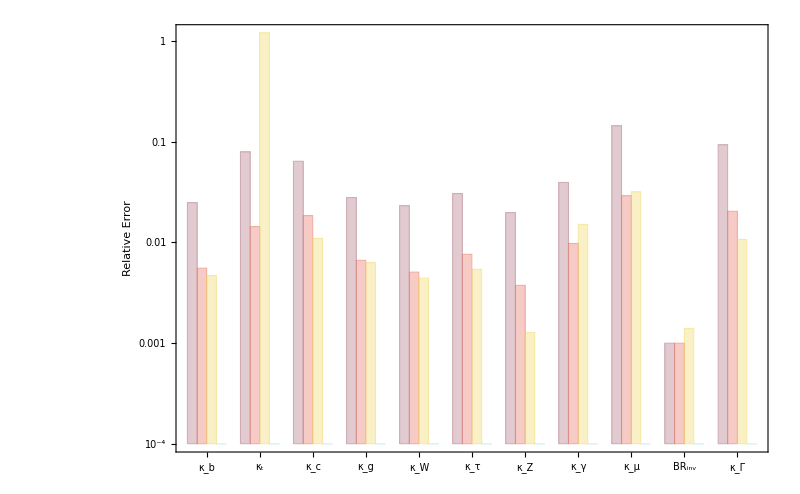

```mathematica
data1={MuC310pdata[[1]],MuC1010pdata[[1]],cepc36010pdata[[1]],MuC10cepc360LHC10pdata[[5]]};
plot=Table[Table[data1[[j,i]],{i,1,Length[data1[[1]]],1}],{j,1,Length[data1],1}];
p10fit1=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_t","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ",Style["\!\(\*SubscriptBox[\(BR\), \(inv\)]\)",25],"κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (10-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,10},{j,-4,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{ColorData[24][8],ColorData[24][1],ColorData[24][3],ColorData[24][4]}},BaseStyle->28,PlotRange->{{1,61},{1*10^-4,1.2}},BarSpacing->{0,1.5},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ImageSize->800]
```

### MuC10TeV+HLLHC, CEPC240GeV+HLLHC, CEPC240+360GeV+HLLHC, MuC10TeV+CEPC240+360GeV+HLLHC+MuC125GeV

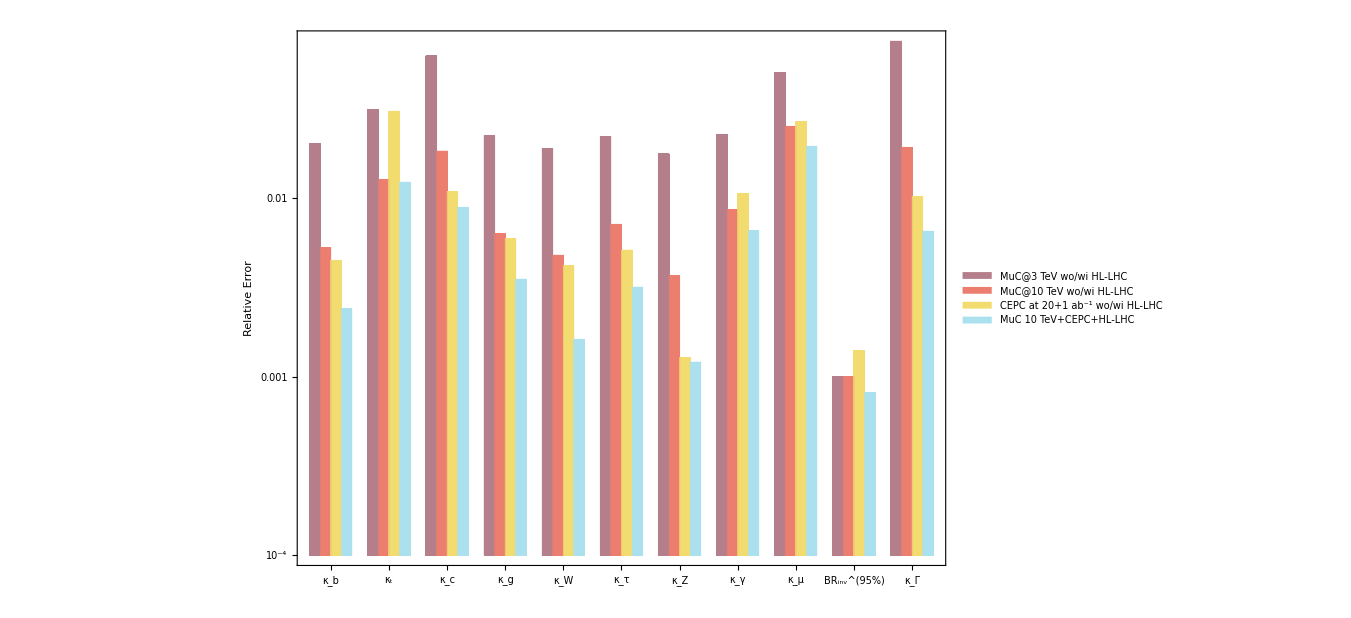

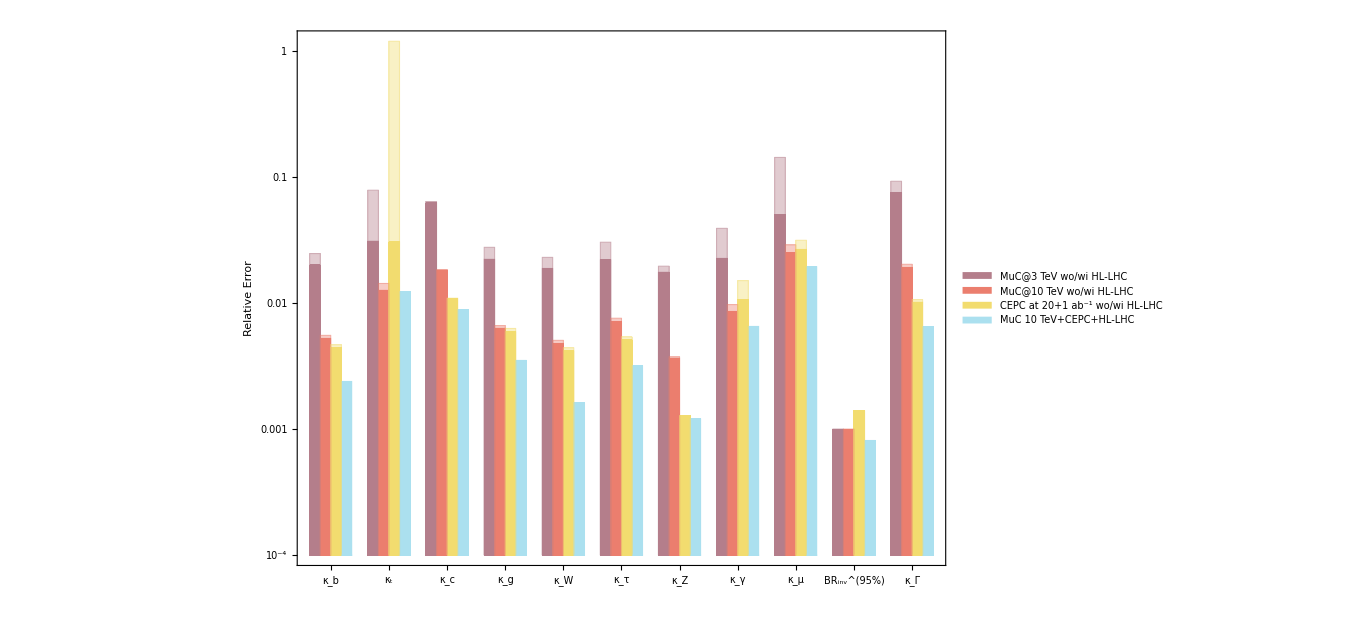

```mathematica
data2={MuC310pdata[[2]],MuC1010pdata[[2]],cepc36010pdata[[2]],MuC10cepc360LHC10pdata[[2]]};
plot=Table[Table[data2[[j,i]],{i,1,Length[data2[[1]]],1}],{j,1,Length[data2],1}];
p10fit2=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_t","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ",Style["\!\(\*SubsuperscriptBox[\(BR\), \(inv\), \(95%\)]\)",25],"κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (11-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,10},{j,-4,1}],1]},ChartStyle->{ColorData[24][8],ColorData[24][1],ColorData[24][3],ColorData[24][4]},BaseStyle->28,PlotRange->{{1,62},{1*10^-4,1.2}},BarSpacing->{0,1.5},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ImageSize->1000,ChartLegends->Placed[{Style["MuC@3 TeV wo/wi HL-LHC",18],Style["MuC@10 TeV wo/wi HL-LHC",18],Style["CEPC at 20+1 ab^-1 wo/wi HL-LHC",18],Style["MuC 10 TeV+CEPC+HL-LHC",18]},Scaled[{{0.22,0.64},{0,0}}]]]
Show[p10fit2,p10fit1]
```

### only MuC 3TeV, only MuC 10TeV, only CEPC 240GeV

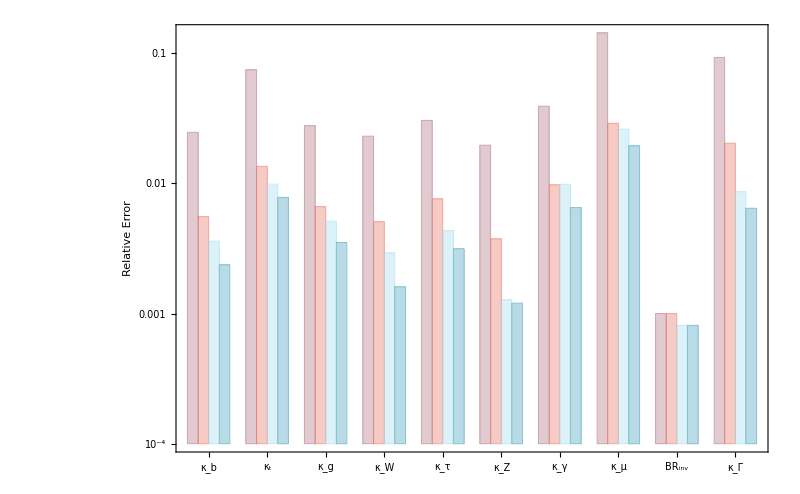

```mathematica
data1={MuC3MuC12510pdata[[1]],MuC10MuC12510pdata[[1]],MuC10cepc360LHC10pdata[[1]],MuC10cepc360LHC10pdata[[2]]};
plot=Table[Table[data1[[j,i]],{i,1,Length[data1[[1]]],1}],{j,1,Length[data1],1}];
p10fit1=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_t","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ",Style["\!\(\*SubsuperscriptBox[\(BR\), \(inv\), \(95%\)]\)",25],"κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (10-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,11},{j,-4,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{ColorData[24][8],ColorData[24][1],ColorData[24][4],ColorData[24][5]}},BaseStyle->28,PlotRange->{{1,55},{1*10^-4,0.5}},BarSpacing->{0,1.5},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ImageSize->800]
```

### MuC3TeV+125GeV, MuC10TeV+125GeV, CEPC240GeV+360GeV

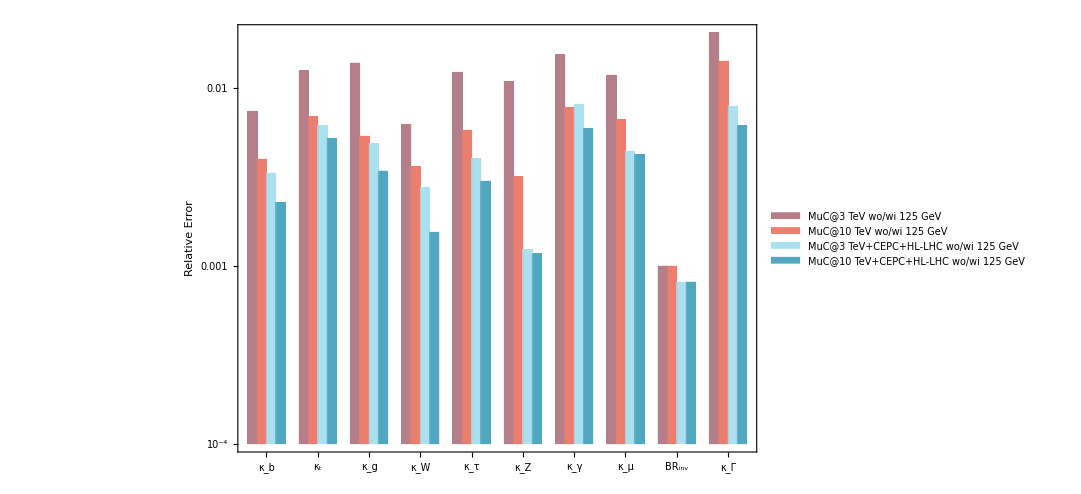

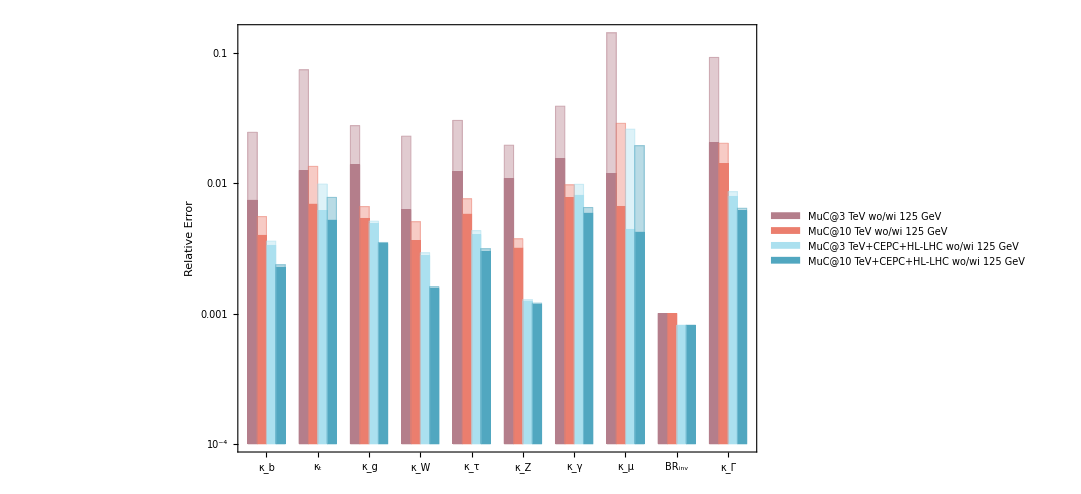

```mathematica
data2={MuC3MuC12510pdata[[2]],MuC10MuC12510pdata[[2]],MuC10cepc360LHC10pdata[[3]],MuC10cepc360LHC10pdata[[4]]};
plot=Table[Table[data2[[j,i]],{i,1,Length[data2[[1]]],1}],{j,1,Length[data2],1}];
p10fit2=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_t","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ",Style["\!\(\*SubscriptBox[\(BR\), \(inv\)]\)",25],"κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (10-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,11},{j,-4,1}],1]},ChartStyle->{ColorData[24][8],ColorData[24][1],ColorData[24][4],ColorData[24][5]},BaseStyle->28,PlotRange->{{1,55},{1*10^-4,1}},BarSpacing->{0,1.5},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ImageSize->800,ChartLegends->Placed[{Style["MuC@3 TeV wo/wi 125 GeV",18],Style["MuC@10 TeV wo/wi 125 GeV",18],Style["MuC@3 TeV+CEPC+HL-LHC wo/wi 125 GeV",18],Style["MuC@10 TeV+CEPC+HL-LHC wo/wi 125 GeV",18]},Scaled[{{0.14,0.55},{0,0}}]]]
Show[p10fit2,p10fit1]
```